```mathematica
β[ω_,δ_,t_,ϵ_]:=
β[ω,δ,t,ϵ]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[14],Join[Table[{i,i-1},{i,Range[2,14,1]}],Table[{i,i+1},{i,Range[1,14,1]}],Table[{2n-1,14-2n+2},{n,4}],Table[{14-2n+2,2n-1},{n,3}]]->-t]
```

```mathematica
T1[t_]:=T1[t]=ReplacePart[0*IdentityMatrix[14],Table[{2n,14-2n+1},{n,3}]->t]
```

```mathematica
TT[t_]:=ReplacePart[0*IdentityMatrix[14],Table[{2n,2n},{n,3}]->t]
```

```mathematica
LEFT[ω_,δ_,t_,ϵ_]:=LEFT[ω,δ,t,ϵ]=Module[{J=Inverse[β[ω,0.0001,1,0]],B:=Inverse[β[ω,0.0001,1,0]],T1:=T1[1]},Do[J=Inverse[IdentityMatrix[14]-B.ConjugateTranspose[T1].J.T1].B,100000]; J=J]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ]]
```

```mathematica
SR[ω_,δ_,t_,ϵ_]:=SR[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
SL[ω_,δ_,t_,ϵ_]:=SL[ω,δ,t,ϵ]=Inverse[IdentityMatrix[14]-g[ω,δ,t,ϵ].ConjugateTranspose[T1[t]].LEFT[ω,δ,t,ϵ].T1[t]].g[ω,δ,t,ϵ]
```

```mathematica
IL[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SL[ω,δ,t,ϵ].TT[t].SR[ω,δ,t,ϵ].TT[t]].SL[ω,δ,t,ϵ]
```

```mathematica
IR[ω_,δ_,t_,ϵ_]:=Inverse[IdentityMatrix[14]-SR[ω,δ,t,ϵ].TT[t].SL[ω,δ,t,ϵ].TT[t]].SR[ω,δ,t,ϵ]
```

```mathematica
gdd[ω_,δ_,t_,ϵ_]:= IL[ω,δ,t,ϵ]-ConjugateTranspose[IL[ω,δ,t,ϵ]]
```

```mathematica
grr[ω_,δ_,t_,ϵ_]:= IR[ω,δ,t,ϵ]-ConjugateTranspose[IR[ω,δ,t,ϵ]]
```

```mathematica
Gnonlocal[ω_,δ_,t_,ϵ_]:= SR[ω,δ,t,ϵ].TT[t].IL[ω,δ,t,ϵ]
```

```mathematica
GNON[ω_,δ_,t_,ϵ_]:= Gnonlocal[ω,δ,t,ϵ]-ConjugateTranspose[Gnonlocal[ω,δ,t,ϵ]]
```

```mathematica
tr[ω_,δ_,t_,ϵ_]:= Abs[Tr[gdd[ω,δ,t,ϵ].TT[t].grr[ω,δ,t,ϵ].TT[t]-TT[t].GNON[ω,δ,t,ϵ].TT[t].GNON[ω,δ,t,ϵ]]]
```

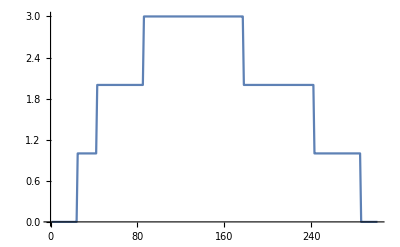

```mathematica
ListLinePlot[Table[tr[ω,0.0001,1,0],{ω,0,3,0.01}]]
```

```mathematica
m05[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp14,imp4,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp1,imp,imp,imp,imp,imp8,imp9,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp7,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m0505= Compile[{ω,ϵ1,ϵ2},m05[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Table[{ω,Mean[ParallelTable[m0505[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,6.43022×10^-7},{0.01,1.48392×10^-6},{0.02,2.93966×10^-6},{0.03,6.29832×10^-6},{0.04,0.0000100325},{0.05,0.0000159008},{0.06,0.0000251844},{0.07,0.0000329007},{0.08,0.0000408124},{0.09,0.0000566903},{0.1,0.0000709241},{0.11,0.0000917754},{0.12,0.000104177},{0.13,0.000133227},{0.14,0.000176792},{0.15,0.000215835},{0.16,0.000296097},{0.17,0.000327568},{0.18,0.000442248},{0.19,0.000507048},{0.2,0.000817387},{0.21,0.00121965},{0.22,0.00195919},{0.23,0.00642348},{0.24,0.269055},{0.25,0.431784},{0.26,0.547424},{0.27,0.628891},{0.28,0.673654},{0.29,0.703624},{0.3,0.732719},{0.31,0.755085},{0.32,0.766238},{0.33,0.772995},{0.34,0.787063},{0.35,0.798987},{0.36,0.805793},{0.37,0.811124},{0.38,0.811674},{0.39,0.816786},{0.4,0.804793},{0.41,0.752635},{0.42,1.21497},{0.43,0.800171},{0.44,0.786982},{0.45,0.893556},{0.46,0.978986},{0.47,1.08098},{0.48,1.14607},{0.49,1.21256},{0.5,1.25626},{0.51,1.30019},{0.52,1.33012},{0.53,1.36722},{0.54,1.39917},{0.55,1.4132},{0.56,1.43608},{0.57,1.45475},{0.58,1.47054},{0.59,1.47602},{0.6,1.48992},{0.61,1.50229},{0.62,1.52308},{0.63,1.52713},{0.64,1.54153},{0.65,1.54262},{0.66,1.55717},{0.67,1.56823},{0.68,1.57811},{0.69,1.57944},{0.7,1.58716},{0.71,1.59706},{0.72,1.60121},{0.73,1.60345},{0.74,1.62155},{0.75,1.6342},{0.76,1.63188},{0.77,1.64961},{0.78,1.6573},{0.79,1.66182},{0.8,1.6724},{0.81,1.68201},{0.82,1.69538},{0.83,1.69898},{0.84,1.69191},{0.85,1.29472},{0.86,1.00193},{0.87,1.16793},{0.88,1.31947},{0.89,1.5175},{0.9,1.65224},{0.91,1.78185},{0.92,1.83899},{0.93,1.9167},{0.94,1.97384},{0.95,2.0304},{0.96,2.08103},{0.97,2.09724},{0.98,2.15047},{0.99,2.17124},{1.,2.19293},{1.01,2.16426},{1.02,2.16229},{1.03,2.16116},{1.04,2.11352},{1.05,1.99088},{1.06,1.80943},{1.07,1.58036},{1.08,1.29904},{1.09,1.00674},{1.1,0.769971},{1.11,0.640918},{1.12,0.6288},{1.13,0.673424},{1.14,0.744897},{1.15,0.825879},{1.16,0.903413},{1.17,1.00989},{1.18,1.07295},{1.19,1.14893},{1.2,1.21798},{1.21,1.26938},{1.22,1.3153},{1.23,1.36493},{1.24,1.37652},{1.25,1.42747},{1.26,1.45021},{1.27,1.46468},{1.28,1.49184},{1.29,1.49919},{1.3,1.51487},{1.31,1.54175},{1.32,1.55673},{1.33,1.56862},{1.34,1.58408},{1.35,1.56939},{1.36,1.58694},{1.37,1.58072},{1.38,1.58966},{1.39,1.58725},{1.4,1.60793},{1.41,1.59191},{1.42,1.58916},{1.43,1.5918},{1.44,1.58879},{1.45,1.58481},{1.46,1.58415},{1.47,1.57983},{1.48,1.57385},{1.49,1.5801},{1.5,1.56481},{1.51,1.54423},{1.52,1.55205},{1.53,1.52456},{1.54,1.53571},{1.55,1.51824},{1.56,1.50539},{1.57,1.49286},{1.58,1.4603},{1.59,1.46446},{1.6,1.43948},{1.61,1.40597},{1.62,1.38489},{1.63,1.3675},{1.64,1.34355},{1.65,1.3204},{1.66,1.29039},{1.67,1.2471},{1.68,1.20847},{1.69,1.13812},{1.7,1.10838},{1.71,1.0482},{1.72,0.982693},{1.73,0.911281},{1.74,0.856755},{1.75,0.845818},{1.76,1.1234},{1.77,1.45628},{1.78,0.995676},{1.79,0.963658},{1.8,0.921475},{1.81,0.787088},{1.82,0.707116},{1.83,0.659185},{1.84,0.704734},{1.85,0.705744},{1.86,0.756154},{1.87,0.795709},{1.88,0.856618},{1.89,0.893226},{1.9,0.923756},{1.91,0.957484},{1.92,0.977584},{1.93,0.998065},{1.94,1.03832},{1.95,1.04459},{1.96,1.04676},{1.97,1.06979},{1.98,1.07371},{1.99,1.07714},{2.,1.09147},{2.01,1.09205},{2.02,1.09615},{2.03,1.08629},{2.04,1.09552},{2.05,1.0956},{2.06,1.09916},{2.07,1.1052},{2.08,1.10611},{2.09,1.09427},{2.1,1.08383},{2.11,1.09019},{2.12,1.07784},{2.13,1.07052},{2.14,1.06991},{2.15,1.05521},{2.16,1.04969},{2.17,1.05381},{2.18,1.04727},{2.19,1.03615},{2.2,1.02935},{2.21,1.02197},{2.22,1.00501},{2.23,0.991389},{2.24,0.969178},{2.25,0.974283},{2.26,0.954994},{2.27,0.939695},{2.28,0.910098},{2.29,0.894267},{2.3,0.884701},{2.31,0.84497},{2.32,0.821869},{2.33,0.80125},{2.34,0.762529},{2.35,0.737247},{2.36,0.704883},{2.37,0.672022},{2.38,0.609632},{2.39,0.589169},{2.4,0.575265},{2.41,0.620885},{2.42,0.643365},{2.43,0.601463},{2.44,1.19863},{2.45,0.478995},{2.46,0.373612},{2.47,0.290658},{2.48,0.235438},{2.49,0.364793},{2.5,0.299308},{2.51,0.329366},{2.52,0.342598},{2.53,0.367961},{2.54,0.375192},{2.55,0.382623},{2.56,0.403192},{2.57,0.420602},{2.58,0.418522},{2.59,0.426768},{2.6,0.424443},{2.61,0.428953},{2.62,0.421861},{2.63,0.425894},{2.64,0.420379},{2.65,0.41163},{2.66,0.402948},{2.67,0.403256},{2.68,0.404217},{2.69,0.389531},{2.7,0.374417},{2.71,0.360035},{2.72,0.357023},{2.73,0.33654},{2.74,0.325082},{2.75,0.32511},{2.76,0.294705},{2.77,0.289164},{2.78,0.269376},{2.79,0.248214},{2.8,0.240756},{2.81,0.225299},{2.82,0.197129},{2.83,0.194691},{2.84,0.186669},{2.85,0.477686},{2.86,0.0150292},{2.87,0.0418336},{2.88,0.0129185},{2.89,0.00370971},{2.9,0.0395559},{2.91,0.000892735},{2.92,0.0201808},{2.93,0.000678377},{2.94,0.000605212},{2.95,0.000303254},{2.96,0.000285322},{2.97,0.000306998},{2.98,0.000368462},{2.99,0.000270133},{3.,0.0000788032}}

```mathematica
Table[{ω,Mean[ParallelTable[m0505[ω,0.3,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,7.01155×10^-7},{0.01,1.81193×10^-6},{0.02,4.09573×10^-6},{0.03,7.38024×10^-6},{0.04,0.0000116872},{0.05,0.0000200599},{0.06,0.0000253094},{0.07,0.0000305433},{0.08,0.0000403701},{0.09,0.0000685043},{0.1,0.0000677729},{0.11,0.0000731151},{0.12,0.000114583},{0.13,0.000149498},{0.14,0.000166028},{0.15,0.000254552},{0.16,0.000262348},{0.17,0.000399048},{0.18,0.000460202},{0.19,0.000545419},{0.2,0.000714258},{0.21,0.00133117},{0.22,0.00253136},{0.23,0.00595187},{0.24,0.245019},{0.25,0.396828},{0.26,0.514785},{0.27,0.584259},{0.28,0.632665},{0.29,0.677335},{0.3,0.699183},{0.31,0.728472},{0.32,0.739342},{0.33,0.758183},{0.34,0.767795},{0.35,0.775828},{0.36,0.78587},{0.37,0.789089},{0.38,0.798659},{0.39,0.798041},{0.4,0.784786},{0.41,0.722761},{0.42,1.29894},{0.43,0.833899},{0.44,0.755862},{0.45,0.833846},{0.46,0.928292},{0.47,1.01125},{0.48,1.07492},{0.49,1.15183},{0.5,1.20605},{0.51,1.24842},{0.52,1.2683},{0.53,1.29907},{0.54,1.34841},{0.55,1.35602},{0.56,1.38041},{0.57,1.39406},{0.58,1.41501},{0.59,1.42684},{0.6,1.43838},{0.61,1.45834},{0.62,1.47076},{0.63,1.48504},{0.64,1.49429},{0.65,1.50301},{0.66,1.50531},{0.67,1.52523},{0.68,1.52843},{0.69,1.52897},{0.7,1.54828},{0.71,1.55535},{0.72,1.56272},{0.73,1.56754},{0.74,1.58098},{0.75,1.59289},{0.76,1.59067},{0.77,1.60664},{0.78,1.61108},{0.79,1.61642},{0.8,1.6299},{0.81,1.64346},{0.82,1.65229},{0.83,1.66636},{0.84,1.64871},{0.85,1.26569},{0.86,0.987295},{0.87,1.04924},{0.88,1.22411},{0.89,1.40119},{0.9,1.53142},{0.91,1.63566},{0.92,1.73145},{0.93,1.80702},{0.94,1.88069},{0.95,1.92529},{0.96,1.9716},{0.97,2.03522},{0.98,2.06129},{0.99,2.08624},{1.,2.10388},{1.01,2.15572},{1.02,2.08616},{1.03,1.6303},{1.04,0.702},{1.05,1.42946},{1.06,1.54747},{1.07,1.42246},{1.08,1.18824},{1.09,0.945701},{1.1,0.722082},{1.11,0.63171},{1.12,0.591235},{1.13,0.638045},{1.14,0.703023},{1.15,0.797125},{1.16,0.889352},{1.17,0.974475},{1.18,1.03669},{1.19,1.09471},{1.2,1.16037},{1.21,1.19966},{1.22,1.26611},{1.23,1.30041},{1.24,1.34322},{1.25,1.36437},{1.26,1.38739},{1.27,1.41069},{1.28,1.42268},{1.29,1.45399},{1.3,1.45789},{1.31,1.47528},{1.32,1.47348},{1.33,1.49843},{1.34,1.49922},{1.35,1.51351},{1.36,1.5179},{1.37,1.5211},{1.38,1.5253},{1.39,1.51863},{1.4,1.52259},{1.41,1.53118},{1.42,1.53302},{1.43,1.51381},{1.44,1.51451},{1.45,1.51445},{1.46,1.5068},{1.47,1.51995},{1.48,1.48856},{1.49,1.49189},{1.5,1.49832},{1.51,1.4631},{1.52,1.47219},{1.53,1.46355},{1.54,1.44236},{1.55,1.4184},{1.56,1.41123},{1.57,1.40777},{1.58,1.38876},{1.59,1.37311},{1.6,1.34887},{1.61,1.31997},{1.62,1.30859},{1.63,1.28298},{1.64,1.25253},{1.65,1.21698},{1.66,1.18043},{1.67,1.1275},{1.68,1.09951},{1.69,1.04629},{1.7,0.991286},{1.71,0.945356},{1.72,0.883587},{1.73,0.821473},{1.74,0.787573},{1.75,0.788347},{1.76,1.2515},{1.77,3.0884},{1.78,1.14487},{1.79,0.877929},{1.8,0.876815},{1.81,0.801153},{1.82,0.771179},{1.83,0.687105},{1.84,0.722845},{1.85,0.688877},{1.86,0.732929},{1.87,0.783973},{1.88,0.839756},{1.89,0.866978},{1.9,0.896957},{1.91,0.933724},{1.92,0.949179},{1.93,0.973685},{1.94,0.997244},{1.95,1.01984},{1.96,1.02069},{1.97,1.04375},{1.98,1.04765},{1.99,1.05253},{2.,1.05047},{2.01,1.05644},{2.02,1.05455},{2.03,1.07083},{2.04,1.06456},{2.05,1.06737},{2.06,1.05014},{2.07,1.06855},{2.08,1.05757},{2.09,1.04805},{2.1,1.05663},{2.11,1.05455},{2.12,1.0344},{2.13,1.04459},{2.14,1.03422},{2.15,1.02885},{2.16,1.02444},{2.17,1.0016},{2.18,1.00351},{2.19,0.988984},{2.2,0.981224},{2.21,0.968013},{2.22,0.961285},{2.23,0.950229},{2.24,0.933765},{2.25,0.929557},{2.26,0.896664},{2.27,0.880781},{2.28,0.870255},{2.29,0.853462},{2.3,0.832708},{2.31,0.799362},{2.32,0.784614},{2.33,0.753087},{2.34,0.712327},{2.35,0.680788},{2.36,0.654884},{2.37,0.616496},{2.38,0.575161},{2.39,0.545462},{2.4,0.519295},{2.41,0.63657},{2.42,1.65497},{2.43,0.546107},{2.44,0.925953},{2.45,0.469937},{2.46,0.37377},{2.47,0.276207},{2.48,0.311101},{2.49,0.295229},{2.5,0.285504},{2.51,0.321875},{2.52,0.339794},{2.53,0.355622},{2.54,0.374797},{2.55,0.387158},{2.56,0.383514},{2.57,0.401492},{2.58,0.415962},{2.59,0.40064},{2.6,0.403202},{2.61,0.413412},{2.62,0.400598},{2.63,0.406468},{2.64,0.405475},{2.65,0.395792},{2.66,0.390698},{2.67,0.385547},{2.68,0.384789},{2.69,0.362698},{2.7,0.361783},{2.71,0.351871},{2.72,0.34464},{2.73,0.326062},{2.74,0.314029},{2.75,0.307147},{2.76,0.279617},{2.77,0.273062},{2.78,0.252556},{2.79,0.248286},{2.8,0.211241},{2.81,0.214093},{2.82,0.194553},{2.83,0.17414},{2.84,0.165521},{2.85,0.364437},{2.86,0.297626},{2.87,0.102138},{2.88,0.0149865},{2.89,0.0482067},{2.9,0.209802},{2.91,0.00162322},{2.92,0.000557457},{2.93,0.00101669},{2.94,0.00117191},{2.95,0.000318028},{2.96,0.00012414},{2.97,0.000122792},{2.98,0.0000963002},{2.99,0.000184385},{3.,0.000211778}}

```mathematica
Table[{ω,Mean[ParallelTable[m0505[ω,0.5,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,7.04936×10^-7},{0.01,2.07936×10^-6},{0.02,4.47691×10^-6},{0.03,8.06855×10^-6},{0.04,0.0000138602},{0.05,0.0000175727},{0.06,0.0000329761},{0.07,0.0000390451},{0.08,0.0000475711},{0.09,0.000077546},{0.1,0.0000850443},{0.11,0.0000900011},{0.12,0.000132035},{0.13,0.000165031},{0.14,0.0001885},{0.15,0.000280702},{0.16,0.000340626},{0.17,0.000374897},{0.18,0.000585834},{0.19,0.000689556},{0.2,0.00101164},{0.21,0.00152706},{0.22,0.00214622},{0.23,0.00834803},{0.24,0.201304},{0.25,0.32998},{0.26,0.469816},{0.27,0.539992},{0.28,0.597426},{0.29,0.632859},{0.3,0.664001},{0.31,0.679882},{0.32,0.708663},{0.33,0.718634},{0.34,0.722641},{0.35,0.739174},{0.36,0.746642},{0.37,0.755342},{0.38,0.761487},{0.39,0.762556},{0.4,0.740839},{0.41,0.669464},{0.42,1.37913},{0.43,0.907798},{0.44,0.732304},{0.45,0.73959},{0.46,0.814372},{0.47,0.907444},{0.48,0.977521},{0.49,1.03601},{0.5,1.09991},{0.51,1.13355},{0.52,1.15719},{0.53,1.20842},{0.54,1.23058},{0.55,1.27344},{0.56,1.29174},{0.57,1.30201},{0.58,1.33534},{0.59,1.33406},{0.6,1.36938},{0.61,1.3761},{0.62,1.40384},{0.63,1.40187},{0.64,1.42933},{0.65,1.42739},{0.66,1.44524},{0.67,1.44669},{0.68,1.45396},{0.69,1.47123},{0.7,1.48079},{0.71,1.48657},{0.72,1.49809},{0.73,1.49585},{0.74,1.51429},{0.75,1.52372},{0.76,1.52732},{0.77,1.54243},{0.78,1.55138},{0.79,1.56233},{0.8,1.56059},{0.81,1.58259},{0.82,1.59337},{0.83,1.60015},{0.84,1.5836},{0.85,1.28414},{0.86,0.969027},{0.87,0.935444},{0.88,1.06006},{0.89,1.21795},{0.9,1.35249},{0.91,1.45914},{0.92,1.56479},{0.93,1.65026},{0.94,1.72943},{0.95,1.78738},{0.96,1.85686},{0.97,1.88819},{0.98,1.94774},{0.99,1.96507},{1.,1.98047},{1.01,2.04904},{1.02,1.98619},{1.03,1.8913},{1.04,1.67658},{1.05,1.17294},{1.06,0.609824},{1.07,0.563726},{1.08,0.68933},{1.09,0.650026},{1.1,0.579088},{1.11,0.529749},{1.12,0.519727},{1.13,0.552279},{1.14,0.61586},{1.15,0.694675},{1.16,0.786053},{1.17,0.859562},{1.18,0.906469},{1.19,0.976303},{1.2,1.04754},{1.21,1.08643},{1.22,1.13701},{1.23,1.17763},{1.24,1.20273},{1.25,1.23301},{1.26,1.2499},{1.27,1.27372},{1.28,1.2921},{1.29,1.31167},{1.3,1.33933},{1.31,1.33965},{1.32,1.34069},{1.33,1.35739},{1.34,1.36253},{1.35,1.37138},{1.36,1.37598},{1.37,1.38444},{1.38,1.38136},{1.39,1.39096},{1.4,1.38649},{1.41,1.38192},{1.42,1.39162},{1.43,1.38558},{1.44,1.38252},{1.45,1.37451},{1.46,1.36871},{1.47,1.36749},{1.48,1.3628},{1.49,1.35212},{1.5,1.3411},{1.51,1.33973},{1.52,1.33067},{1.53,1.30288},{1.54,1.29333},{1.55,1.28713},{1.56,1.26293},{1.57,1.24551},{1.58,1.24062},{1.59,1.21855},{1.6,1.20217},{1.61,1.17406},{1.62,1.15182},{1.63,1.12553},{1.64,1.09813},{1.65,1.06936},{1.66,1.02614},{1.67,0.999248},{1.68,0.941489},{1.69,0.903176},{1.7,0.854014},{1.71,0.795275},{1.72,0.759147},{1.73,0.723694},{1.74,0.714923},{1.75,0.790428},{1.76,1.34481},{1.77,2.32998},{1.78,1.80092},{1.79,1.11671},{1.8,0.901859},{1.81,0.832286},{1.82,0.727345},{1.83,0.624142},{1.84,0.615649},{1.85,0.62667},{1.86,0.674314},{1.87,0.702553},{1.88,0.778688},{1.89,0.800435},{1.9,0.844578},{1.91,0.862121},{1.92,0.898386},{1.93,0.911641},{1.94,0.932616},{1.95,0.942407},{1.96,0.961691},{1.97,0.970953},{1.98,0.974638},{1.99,0.979022},{2.,0.978504},{2.01,0.993472},{2.02,0.979817},{2.03,0.988249},{2.04,0.993247},{2.05,0.985246},{2.06,0.998667},{2.07,0.988907},{2.08,0.983364},{2.09,0.978122},{2.1,0.975117},{2.11,0.968156},{2.12,0.97041},{2.13,0.947378},{2.14,0.955193},{2.15,0.952496},{2.16,0.932096},{2.17,0.921743},{2.18,0.913261},{2.19,0.902152},{2.2,0.899296},{2.21,0.883283},{2.22,0.882491},{2.23,0.861627},{2.24,0.860742},{2.25,0.840116},{2.26,0.815757},{2.27,0.795548},{2.28,0.787368},{2.29,0.768027},{2.3,0.741324},{2.31,0.725668},{2.32,0.684843},{2.33,0.669848},{2.34,0.639132},{2.35,0.611678},{2.36,0.574163},{2.37,0.544715},{2.38,0.514887},{2.39,0.486466},{2.4,0.510345},{2.41,0.670496},{2.42,1.57173},{2.43,0.996383},{2.44,1.06084},{2.45,0.480001},{2.46,0.380438},{2.47,0.250116},{2.48,0.213823},{2.49,0.266234},{2.5,0.288346},{2.51,0.294971},{2.52,0.306622},{2.53,0.333339},{2.54,0.34354},{2.55,0.348802},{2.56,0.359544},{2.57,0.372154},{2.58,0.374071},{2.59,0.384216},{2.6,0.372445},{2.61,0.372521},{2.62,0.367194},{2.63,0.383772},{2.64,0.374375},{2.65,0.362994},{2.66,0.363248},{2.67,0.353575},{2.68,0.350495},{2.69,0.338339},{2.7,0.336272},{2.71,0.321396},{2.72,0.308577},{2.73,0.298884},{2.74,0.290008},{2.75,0.268208},{2.76,0.253628},{2.77,0.247388},{2.78,0.232202},{2.79,0.216755},{2.8,0.203861},{2.81,0.182809},{2.82,0.175437},{2.83,0.153594},{2.84,0.156649},{2.85,1.7217},{2.86,0.816223},{2.87,0.398409},{2.88,0.00393436},{2.89,0.00715829},{2.9,0.00959094},{2.91,0.0890604},{2.92,0.00557258},{2.93,0.00157982},{2.94,0.0325374},{2.95,0.000793456},{2.96,0.000556326},{2.97,0.000556393},{2.98,0.000241695},{2.99,0.000218267},{3.,0.000115883}}

```mathematica
Table[{ω,Mean[ParallelTable[m0505[ω,0.7,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,2.97509×10^-7},{0.01,6.52826×10^-6},{0.02,4.76132×10^-6},{0.03,9.46989×10^-6},{0.04,0.000016268},{0.05,0.0000215072},{0.06,0.0000319184},{0.07,0.0000528957},{0.08,0.0000643527},{0.09,0.0000877555},{0.1,0.0000933802},{0.11,0.000123329},{0.12,0.000165982},{0.13,0.00018583},{0.14,0.00024187},{0.15,0.000277497},{0.16,0.000368337},{0.17,0.000501596},{0.18,0.000703936},{0.19,0.000762145},{0.2,0.00103937},{0.21,0.00178391},{0.22,0.00288701},{0.23,0.00872904},{0.24,0.193417},{0.25,0.284686},{0.26,0.404752},{0.27,0.479873},{0.28,0.542338},{0.29,0.577765},{0.3,0.609255},{0.31,0.639772},{0.32,0.661116},{0.33,0.678637},{0.34,0.690817},{0.35,0.700123},{0.36,0.71288},{0.37,0.720786},{0.38,0.722651},{0.39,0.722524},{0.4,0.714787},{0.41,0.639178},{0.42,1.44629},{0.43,0.983047},{0.44,0.771555},{0.45,0.699269},{0.46,0.737073},{0.47,0.798366},{0.48,0.874373},{0.49,0.924951},{0.5,0.976474},{0.51,1.01677},{0.52,1.05791},{0.53,1.11125},{0.54,1.12359},{0.55,1.15947},{0.56,1.19475},{0.57,1.2139},{0.58,1.23176},{0.59,1.24477},{0.6,1.28158},{0.61,1.283},{0.62,1.29446},{0.63,1.31608},{0.64,1.32227},{0.65,1.34832},{0.66,1.35672},{0.67,1.36586},{0.68,1.37313},{0.69,1.3824},{0.7,1.39506},{0.71,1.40519},{0.72,1.41386},{0.73,1.43534},{0.74,1.42998},{0.75,1.45475},{0.76,1.45379},{0.77,1.46123},{0.78,1.47975},{0.79,1.47801},{0.8,1.48599},{0.81,1.50737},{0.82,1.51604},{0.83,1.52434},{0.84,1.51211},{0.85,1.32187},{0.86,1.03518},{0.87,0.857732},{0.88,0.936085},{0.89,1.06813},{0.9,1.1807},{0.91,1.27569},{0.92,1.41025},{0.93,1.47114},{0.94,1.57289},{0.95,1.61602},{0.96,1.67169},{0.97,1.71957},{0.98,1.77743},{0.99,1.78905},{1.,1.82117},{1.01,1.88555},{1.02,1.85331},{1.03,1.81496},{1.04,1.70507},{1.05,1.48349},{1.06,1.16815},{1.07,0.792395},{1.08,0.492903},{1.09,0.404287},{1.1,0.374793},{1.11,0.370182},{1.12,0.402571},{1.13,0.423809},{1.14,0.487823},{1.15,0.538044},{1.16,0.625991},{1.17,0.686329},{1.18,0.722812},{1.19,0.806487},{1.2,0.860762},{1.21,0.903093},{1.22,0.953049},{1.23,0.980781},{1.24,1.029},{1.25,1.05513},{1.26,1.07657},{1.27,1.06735},{1.28,1.11536},{1.29,1.12981},{1.3,1.14386},{1.31,1.16043},{1.32,1.16816},{1.33,1.17626},{1.34,1.18863},{1.35,1.20325},{1.36,1.19884},{1.37,1.20363},{1.38,1.2174},{1.39,1.21983},{1.4,1.2073},{1.41,1.19483},{1.42,1.2081},{1.43,1.20707},{1.44,1.2012},{1.45,1.21012},{1.46,1.18177},{1.47,1.1871},{1.48,1.16629},{1.49,1.15198},{1.5,1.16655},{1.51,1.14793},{1.52,1.1511},{1.53,1.1388},{1.54,1.13618},{1.55,1.113},{1.56,1.11339},{1.57,1.08019},{1.58,1.05466},{1.59,1.04897},{1.6,1.01859},{1.61,1.01556},{1.62,0.990698},{1.63,0.95669},{1.64,0.93906},{1.65,0.892174},{1.66,0.860172},{1.67,0.811826},{1.68,0.805576},{1.69,0.760808},{1.7,0.716279},{1.71,0.674339},{1.72,0.666033},{1.73,0.652507},{1.74,0.668964},{1.75,0.806488},{1.76,1.43834},{1.77,1.93717},{1.78,1.21535},{1.79,1.1828},{1.8,1.06833},{1.81,0.953328},{1.82,0.714221},{1.83,0.677728},{1.84,0.605826},{1.85,0.575622},{1.86,0.619084},{1.87,0.63703},{1.88,0.657939},{1.89,0.688768},{1.9,0.721145},{1.91,0.755579},{1.92,0.779667},{1.93,0.806061},{1.94,0.817258},{1.95,0.822122},{1.96,0.850834},{1.97,0.844799},{1.98,0.857913},{1.99,0.859279},{2.,0.863428},{2.01,0.863711},{2.02,0.871292},{2.03,0.882994},{2.04,0.872032},{2.05,0.875005},{2.06,0.872147},{2.07,0.866752},{2.08,0.862621},{2.09,0.865208},{2.1,0.864039},{2.11,0.865883},{2.12,0.855131},{2.13,0.84935},{2.14,0.834494},{2.15,0.841927},{2.16,0.828394},{2.17,0.818642},{2.18,0.819618},{2.19,0.798152},{2.2,0.790992},{2.21,0.783669},{2.22,0.764631},{2.23,0.753989},{2.24,0.741703},{2.25,0.736711},{2.26,0.710457},{2.27,0.687168},{2.28,0.692127},{2.29,0.654709},{2.3,0.633745},{2.31,0.606821},{2.32,0.588898},{2.33,0.553493},{2.34,0.541955},{2.35,0.503218},{2.36,0.483783},{2.37,0.465269},{2.38,0.453261},{2.39,0.429689},{2.4,0.477624},{2.41,0.720717},{2.42,1.22037},{2.43,1.04643},{2.44,1.07998},{2.45,1.17324},{2.46,0.53397},{2.47,0.305872},{2.48,0.313418},{2.49,0.24269},{2.5,0.253588},{2.51,0.246927},{2.52,0.269067},{2.53,0.280688},{2.54,0.299704},{2.55,0.299729},{2.56,0.303036},{2.57,0.314095},{2.58,0.315804},{2.59,0.316274},{2.6,0.319492},{2.61,0.316977},{2.62,0.315701},{2.63,0.310476},{2.64,0.320594},{2.65,0.310863},{2.66,0.307701},{2.67,0.294391},{2.68,0.28591},{2.69,0.288276},{2.7,0.275534},{2.71,0.261034},{2.72,0.266036},{2.73,0.250045},{2.74,0.23636},{2.75,0.237891},{2.76,0.210941},{2.77,0.196802},{2.78,0.19075},{2.79,0.174704},{2.8,0.169889},{2.81,0.16417},{2.82,0.144021},{2.83,0.146027},{2.84,0.151146},{2.85,0.691802},{2.86,26.2397},{2.87,0.103216},{2.88,1.10864},{2.89,0.0113852},{2.9,0.0165247},{2.91,0.00145184},{2.92,0.00236669},{2.93,0.0011844},{2.94,0.00107237},{2.95,0.000600503},{2.96,0.000284336},{2.97,0.000151822},{2.98,0.00017925},{2.99,0.000135037},{3.,0.000117135}}

```mathematica
Export["/home/shardulmukim//PhD/fwi/AGNR/7AGNR/two_imp/data_/0.1/na_10_nb_4_per25.dat",%28]
```

/home/shardulmukim//PhD/fwi/AGNR/7AGNR/two_imp/data_/0.3/na_10_nb_4_per25.dat

```mathematica
RandomSample[Join[Flatten[Table[RandomSample[{imp1,imp2,imp3,imp4,imp5,imp6,imp7,imp8,imp9,imp10,imp11,imp12,imp13,imp14}],4 ]],Table[imp,44]]]
```

{imp,imp2,imp12,imp,imp3,imp11,imp,imp9,imp,imp7,imp8,imp,imp1,imp11,imp5,imp,imp6,imp,imp1,imp,imp6,imp,imp9,imp,imp,imp13,imp3,imp,imp6,imp,imp,imp,imp,imp3,imp,imp13,imp,imp9,imp,imp,imp7,imp,imp2,imp,imp5,imp9,imp10,imp7,imp,imp,imp,imp,imp,imp,imp4,imp10,imp10,imp,imp7,imp,imp,imp2,imp14,imp,imp1,imp3,imp,imp14,imp,imp,imp12,imp,imp11,imp,imp,imp8,imp,imp5,imp8,imp12,imp1,imp,imp5,imp2,imp,imp11,imp4,imp13,imp14,imp4,imp10,imp,imp,imp6,imp8,imp4,imp13,imp14,imp,imp12}

```mathematica
m56[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp,imp2,imp12,imp,imp3,imp11,imp,imp9,imp,imp7,imp8,imp,imp1,imp11,imp5,imp,imp6,imp,imp1,imp,imp6,imp,imp9,imp,imp,imp13,imp3,imp,imp6,imp,imp,imp,imp,imp3,imp,imp13,imp,imp9,imp,imp,imp7,imp,imp2,imp,imp5,imp9,imp10,imp7,imp,imp,imp,imp,imp,imp,imp4,imp10,imp10,imp,imp7,imp,imp,imp2,imp14,imp,imp1,imp3,imp,imp14,imp,imp,imp12,imp,imp11,imp,imp,imp8,imp,imp5,imp8,imp12,imp1,imp,imp5,imp2,imp,imp11,imp4,imp13,imp14,imp4,imp10,imp,imp,imp6,imp8,imp4,imp13,imp14,imp,imp12}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m5656= Compile[{ω,ϵ1,ϵ2},m56[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565601.dat",%50]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565601.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565603.dat",%51]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565603.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565605.dat",%52]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565605.dat

```mathematica
Export["/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565607.dat",%53]
```

/home/shardulmukim/PhD/fwi/AGNR/7AGNR/two_imp/data_new/4per/m565607.dat

```mathematica
Table[{ω,Mean[ParallelTable[m5656[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m5656[ω,0.3,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m5656[ω,0.5,0.9],2000]]},{ω,Range[0,3,0.01]}]
Table[{ω,Mean[ParallelTable[m5656[ω,0.7,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,0.0000103283},{0.01,7.72769×10^-6},{0.02,0.000011283},{0.03,0.0000124998},{0.04,0.0000207334},{0.05,0.0000261757},{0.06,0.0000316287},{0.07,0.0000408121},{0.08,0.0000461437},{0.09,0.0000401088},{0.1,0.0000593476},{0.11,0.000069121},{0.12,0.0000872552},{0.13,0.0000853744},{0.14,0.000165144},{0.15,0.000141443},{0.16,0.000166713},{0.17,0.000206225},{0.18,0.000258045},{0.19,0.000335766},{0.2,0.000347635},{0.21,0.000747927},{0.22,0.00107094},{0.23,0.00238717},{0.24,0.0947768},{0.25,0.156461},{0.26,0.189506},{0.27,0.240464},{0.28,0.297607},{0.29,0.344989},{0.3,0.366206},{0.31,0.410906},{0.32,0.427478},{0.33,0.443927},{0.34,0.461312},{0.35,0.480973},{0.36,0.484722},{0.37,0.50523},{0.38,0.50821},{0.39,0.503216},{0.4,0.490827},{0.41,0.514837},{0.42,0.940841},{0.43,1.26608},{0.44,1.083},{0.45,0.85526},{0.46,0.703903},{0.47,0.607726},{0.48,0.57744},{0.49,0.565989},{0.5,0.58711},{0.51,0.596441},{0.52,0.60861},{0.53,0.632799},{0.54,0.660481},{0.55,0.683844},{0.56,0.695154},{0.57,0.728075},{0.58,0.73991},{0.59,0.74162},{0.6,0.781381},{0.61,0.813343},{0.62,0.818535},{0.63,0.839299},{0.64,0.848715},{0.65,0.861594},{0.66,0.900854},{0.67,0.904418},{0.68,0.910243},{0.69,0.935448},{0.7,0.93604},{0.71,0.961626},{0.72,0.978464},{0.73,0.997136},{0.74,0.994985},{0.75,1.01652},{0.76,1.02569},{0.77,1.03448},{0.78,1.05654},{0.79,1.06893},{0.8,1.06886},{0.81,1.0777},{0.82,1.09412},{0.83,1.0779},{0.84,1.00411},{0.85,0.982651},{0.86,1.23988},{0.87,1.00407},{0.88,0.835621},{0.89,0.735054},{0.9,0.718862},{0.91,0.744787},{0.92,0.792801},{0.93,0.827777},{0.94,0.894742},{0.95,0.957123},{0.96,0.995784},{0.97,1.06444},{0.98,1.08261},{0.99,1.10972},{1.,1.14053},{1.01,1.21537},{1.02,1.14556},{1.03,1.14009},{1.04,1.0532},{1.05,0.898807},{1.06,0.692791},{1.07,0.516049},{1.08,0.398277},{1.09,0.33872},{1.1,0.336116},{1.11,0.330533},{1.12,0.335434},{1.13,0.327771},{1.14,0.315509},{1.15,0.32388},{1.16,0.32429},{1.17,0.321609},{1.18,0.327355},{1.19,0.341513},{1.2,0.362967},{1.21,0.355644},{1.22,0.380777},{1.23,0.397738},{1.24,0.416543},{1.25,0.440431},{1.26,0.449344},{1.27,0.437085},{1.28,0.468532},{1.29,0.476881},{1.3,0.479116},{1.31,0.479621},{1.32,0.503723},{1.33,0.49907},{1.34,0.494195},{1.35,0.497703},{1.36,0.508491},{1.37,0.518653},{1.38,0.531915},{1.39,0.518667},{1.4,0.529341},{1.41,0.539688},{1.42,0.541684},{1.43,0.534984},{1.44,0.559349},{1.45,0.525844},{1.46,0.466602},{1.47,0.468047},{1.48,0.497882},{1.49,0.50362},{1.5,0.48892},{1.51,0.501748},{1.52,0.512069},{1.53,0.503945},{1.54,0.50094},{1.55,0.49724},{1.56,0.457246},{1.57,0.428847},{1.58,0.436003},{1.59,0.43488},{1.6,0.442756},{1.61,0.43179},{1.62,0.434881},{1.63,0.426088},{1.64,0.437697},{1.65,0.432696},{1.66,0.437733},{1.67,0.441154},{1.68,0.450275},{1.69,0.46227},{1.7,0.4915},{1.71,0.539434},{1.72,0.609304},{1.73,0.695982},{1.74,0.893731},{1.75,1.32021},{1.76,2.41206},{1.77,2.92042},{1.78,1.79824},{1.79,1.41833},{1.8,1.36781},{1.81,1.50008},{1.82,1.45605},{1.83,1.02196},{1.84,0.844176},{1.85,0.751917},{1.86,0.579566},{1.87,0.452816},{1.88,0.438817},{1.89,0.375764},{1.9,0.35129},{1.91,0.332644},{1.92,0.321961},{1.93,0.295596},{1.94,0.312644},{1.95,0.329335},{1.96,0.34799},{1.97,0.35228},{1.98,0.362315},{1.99,0.369295},{2.,0.377135},{2.01,0.394218},{2.02,0.397192},{2.03,0.402468},{2.04,0.405607},{2.05,0.412495},{2.06,0.41981},{2.07,0.397911},{2.08,0.415305},{2.09,0.404356},{2.1,0.403646},{2.11,0.369165},{2.12,0.328847},{2.13,0.344299},{2.14,0.341571},{2.15,0.354378},{2.16,0.352772},{2.17,0.354207},{2.18,0.336079},{2.19,0.347501},{2.2,0.350471},{2.21,0.33429},{2.22,0.340897},{2.23,0.318745},{2.24,0.318042},{2.25,0.309097},{2.26,0.301872},{2.27,0.301281},{2.28,0.294245},{2.29,0.291474},{2.3,0.27705},{2.31,0.281281},{2.32,0.271859},{2.33,0.274799},{2.34,0.27822},{2.35,0.271282},{2.36,0.284617},{2.37,0.31193},{2.38,0.331588},{2.39,0.382678},{2.4,0.504022},{2.41,1.07799},{2.42,1.29358},{2.43,1.43018},{2.44,2.74892},{2.45,1.07463},{2.46,0.985098},{2.47,1.11398},{2.48,0.737001},{2.49,0.45416},{2.5,0.576922},{2.51,0.302821},{2.52,0.244774},{2.53,0.201856},{2.54,0.198149},{2.55,0.181385},{2.56,0.165695},{2.57,0.160697},{2.58,0.151515},{2.59,0.155362},{2.6,0.15726},{2.61,0.151041},{2.62,0.143151},{2.63,0.139063},{2.64,0.142793},{2.65,0.147324},{2.66,0.141845},{2.67,0.143711},{2.68,0.137065},{2.69,0.13404},{2.7,0.129581},{2.71,0.128093},{2.72,0.119212},{2.73,0.124596},{2.74,0.114141},{2.75,0.119763},{2.76,0.115265},{2.77,0.11089},{2.78,0.115221},{2.79,0.105741},{2.8,0.119693},{2.81,0.107728},{2.82,0.117589},{2.83,0.113388},{2.84,0.121804},{2.85,0.432384},{2.86,0.110476},{2.87,0.754296},{2.88,0.212047},{2.89,0.0167893},{2.9,0.671699},{2.91,0.124359},{2.92,0.0880727},{2.93,1.86198},{2.94,0.00532765},{2.95,0.0380361},{2.96,0.165226},{2.97,0.000796931},{2.98,0.00100873},{2.99,0.000777386},{3.,0.000397209}}

{{0.,0.0000128261},{0.01,9.75876×10^-6},{0.02,9.26806×10^-6},{0.03,8.61504×10^-6},{0.04,0.0000132408},{0.05,0.0000164028},{0.06,0.0000200413},{0.07,0.0000241526},{0.08,0.0000300782},{0.09,0.0000430887},{0.1,0.0000516228},{0.11,0.0000624063},{0.12,0.000068246},{0.13,0.000071783},{0.14,0.0000942888},{0.15,0.000127723},{0.16,0.000115962},{0.17,0.000162286},{0.18,0.000152818},{0.19,0.000278098},{0.2,0.000374464},{0.21,0.000526164},{0.22,0.0007954},{0.23,0.00162189},{0.24,0.0787409},{0.25,0.123627},{0.26,0.171655},{0.27,0.213023},{0.28,0.26299},{0.29,0.307722},{0.3,0.343069},{0.31,0.377461},{0.32,0.389124},{0.33,0.41902},{0.34,0.438996},{0.35,0.437107},{0.36,0.461737},{0.37,0.460372},{0.38,0.472304},{0.39,0.477722},{0.4,0.463944},{0.41,0.497387},{0.42,0.811461},{0.43,1.17811},{0.44,1.09476},{0.45,0.905234},{0.46,0.716907},{0.47,0.627482},{0.48,0.576716},{0.49,0.552367},{0.5,0.543832},{0.51,0.5549},{0.52,0.584754},{0.53,0.580927},{0.54,0.612102},{0.55,0.630414},{0.56,0.649572},{0.57,0.663344},{0.58,0.695453},{0.59,0.697972},{0.6,0.723695},{0.61,0.747081},{0.62,0.752763},{0.63,0.758509},{0.64,0.791864},{0.65,0.82317},{0.66,0.827125},{0.67,0.854451},{0.68,0.84795},{0.69,0.855954},{0.7,0.88048},{0.71,0.895522},{0.72,0.89402},{0.73,0.912154},{0.74,0.934014},{0.75,0.942035},{0.76,0.954908},{0.77,0.952408},{0.78,0.981167},{0.79,0.974513},{0.8,1.00523},{0.81,0.994865},{0.82,0.994781},{0.83,0.985852},{0.84,0.933501},{0.85,0.932486},{0.86,1.14645},{0.87,1.09219},{0.88,0.864797},{0.89,0.73044},{0.9,0.680705},{0.91,0.671786},{0.92,0.695942},{0.93,0.756507},{0.94,0.795104},{0.95,0.856616},{0.96,0.888846},{0.97,0.947979},{0.98,0.984419},{0.99,1.0115},{1.,1.04313},{1.01,1.15297},{1.02,1.05757},{1.03,0.635913},{1.04,0.348717},{1.05,0.479907},{1.06,0.490428},{1.07,0.428753},{1.08,0.364007},{1.09,0.342467},{1.1,0.325351},{1.11,0.331943},{1.12,0.322888},{1.13,0.337226},{1.14,0.326522},{1.15,0.327203},{1.16,0.318547},{1.17,0.321289},{1.18,0.319215},{1.19,0.322283},{1.2,0.344145},{1.21,0.359496},{1.22,0.365387},{1.23,0.388588},{1.24,0.399401},{1.25,0.412105},{1.26,0.426731},{1.27,0.428161},{1.28,0.424636},{1.29,0.444465},{1.3,0.451267},{1.31,0.444795},{1.32,0.459661},{1.33,0.463897},{1.34,0.460122},{1.35,0.465045},{1.36,0.470975},{1.37,0.47697},{1.38,0.481519},{1.39,0.480296},{1.4,0.492472},{1.41,0.483691},{1.42,0.491507},{1.43,0.488844},{1.44,0.500239},{1.45,0.487951},{1.46,0.431358},{1.47,0.431769},{1.48,0.44207},{1.49,0.450205},{1.5,0.452467},{1.51,0.44331},{1.52,0.452843},{1.53,0.444081},{1.54,0.456772},{1.55,0.451961},{1.56,0.423198},{1.57,0.41225},{1.58,0.405916},{1.59,0.408127},{1.6,0.409381},{1.61,0.400296},{1.62,0.415164},{1.63,0.400578},{1.64,0.404996},{1.65,0.423339},{1.66,0.415959},{1.67,0.451821},{1.68,0.446658},{1.69,0.48299},{1.7,0.513306},{1.71,0.57072},{1.72,0.641885},{1.73,0.781041},{1.74,1.00622},{1.75,1.50995},{1.76,2.63502},{1.77,4.1055},{1.78,2.26778},{1.79,1.52803},{1.8,1.44525},{1.81,1.3348},{1.82,1.24653},{1.83,1.05541},{1.84,0.937967},{1.85,0.724727},{1.86,0.591378},{1.87,0.440161},{1.88,0.382535},{1.89,0.377795},{1.9,0.358063},{1.91,0.344702},{1.92,0.304011},{1.93,0.269009},{1.94,0.273481},{1.95,0.304363},{1.96,0.3149},{1.97,0.330473},{1.98,0.33789},{1.99,0.351012},{2.,0.349264},{2.01,0.357389},{2.02,0.366593},{2.03,0.367133},{2.04,0.371988},{2.05,0.374979},{2.06,0.387053},{2.07,0.373168},{2.08,0.384308},{2.09,0.374781},{2.1,0.387884},{2.11,0.35601},{2.12,0.316755},{2.13,0.310054},{2.14,0.306462},{2.15,0.31747},{2.16,0.319722},{2.17,0.321695},{2.18,0.320545},{2.19,0.314473},{2.2,0.321577},{2.21,0.31879},{2.22,0.304537},{2.23,0.299227},{2.24,0.302459},{2.25,0.280984},{2.26,0.278361},{2.27,0.274793},{2.28,0.273911},{2.29,0.272698},{2.3,0.261523},{2.31,0.268227},{2.32,0.258145},{2.33,0.257704},{2.34,0.262842},{2.35,0.26447},{2.36,0.280142},{2.37,0.292606},{2.38,0.347797},{2.39,0.405742},{2.4,0.576333},{2.41,1.20995},{2.42,1.96902},{2.43,1.46325},{2.44,1.4683},{2.45,1.3501},{2.46,1.11667},{2.47,0.8827},{2.48,0.499954},{2.49,0.587553},{2.5,0.424952},{2.51,0.291511},{2.52,0.254882},{2.53,0.211039},{2.54,0.189597},{2.55,0.169057},{2.56,0.164033},{2.57,0.157002},{2.58,0.149042},{2.59,0.145199},{2.6,0.142014},{2.61,0.1413},{2.62,0.143262},{2.63,0.139429},{2.64,0.135512},{2.65,0.130802},{2.66,0.135809},{2.67,0.128635},{2.68,0.131023},{2.69,0.131006},{2.7,0.125992},{2.71,0.12194},{2.72,0.118782},{2.73,0.116507},{2.74,0.12272},{2.75,0.112067},{2.76,0.111472},{2.77,0.104349},{2.78,0.106142},{2.79,0.110277},{2.8,0.109745},{2.81,0.111689},{2.82,0.107448},{2.83,0.123671},{2.84,0.142954},{2.85,0.288136},{2.86,0.0409489},{2.87,0.30394},{2.88,0.803251},{2.89,0.0126209},{2.9,4.96316},{2.91,0.120362},{2.92,0.011454},{2.93,0.292739},{2.94,0.00289224},{2.95,0.00435096},{2.96,0.115047},{2.97,0.000545484},{2.98,0.000561177},{2.99,0.000463852},{3.,0.000526128}}

{{0.,0.0000116543},{0.01,0.0000151652},{0.02,0.0000105316},{0.03,7.74717×10^-6},{0.04,0.0000113202},{0.05,0.0000143364},{0.06,0.0000217809},{0.07,0.0000274957},{0.08,0.0000373905},{0.09,0.000030212},{0.1,0.0000328354},{0.11,0.0000507467},{0.12,0.0000671935},{0.13,0.0000670524},{0.14,0.000062471},{0.15,0.0000800318},{0.16,0.00010854},{0.17,0.000137569},{0.18,0.000118636},{0.19,0.000207381},{0.2,0.000258459},{0.21,0.000423693},{0.22,0.000899176},{0.23,0.00171348},{0.24,0.0788426},{0.25,0.111097},{0.26,0.150854},{0.27,0.189296},{0.28,0.213109},{0.29,0.260774},{0.3,0.308532},{0.31,0.323664},{0.32,0.351952},{0.33,0.367277},{0.34,0.386768},{0.35,0.391135},{0.36,0.405809},{0.37,0.419895},{0.38,0.40393},{0.39,0.413666},{0.4,0.432992},{0.41,0.465227},{0.42,0.857977},{0.43,1.14799},{0.44,1.1439},{0.45,1.00901},{0.46,0.808673},{0.47,0.649938},{0.48,0.599033},{0.49,0.531714},{0.5,0.527475},{0.51,0.505486},{0.52,0.526198},{0.53,0.503319},{0.54,0.539427},{0.55,0.549182},{0.56,0.560284},{0.57,0.576652},{0.58,0.594768},{0.59,0.612774},{0.6,0.63123},{0.61,0.63974},{0.62,0.660916},{0.63,0.671451},{0.64,0.693846},{0.65,0.699162},{0.66,0.721835},{0.67,0.743316},{0.68,0.749731},{0.69,0.756349},{0.7,0.758622},{0.71,0.788351},{0.72,0.794758},{0.73,0.799098},{0.74,0.810776},{0.75,0.833156},{0.76,0.830543},{0.77,0.855894},{0.78,0.855605},{0.79,0.873485},{0.8,0.877124},{0.81,0.87658},{0.82,0.876492},{0.83,0.861543},{0.84,0.792006},{0.85,0.927835},{0.86,1.06903},{0.87,1.13721},{0.88,0.920372},{0.89,0.777609},{0.9,0.667158},{0.91,0.633638},{0.92,0.61895},{0.93,0.632172},{0.94,0.669657},{0.95,0.705864},{0.96,0.764678},{0.97,0.791933},{0.98,0.829719},{0.99,0.870717},{1.,0.892026},{1.01,1.01033},{1.02,0.977263},{1.03,0.841549},{1.04,0.631985},{1.05,0.400345},{1.06,0.341717},{1.07,0.349901},{1.08,0.33342},{1.09,0.339177},{1.1,0.340111},{1.11,0.343291},{1.12,0.337976},{1.13,0.3406},{1.14,0.326262},{1.15,0.319678},{1.16,0.313373},{1.17,0.306659},{1.18,0.314079},{1.19,0.313619},{1.2,0.325314},{1.21,0.322748},{1.22,0.332648},{1.23,0.34525},{1.24,0.343849},{1.25,0.373916},{1.26,0.371995},{1.27,0.365259},{1.28,0.370735},{1.29,0.389976},{1.3,0.392749},{1.31,0.38975},{1.32,0.400587},{1.33,0.381468},{1.34,0.390622},{1.35,0.409558},{1.36,0.389785},{1.37,0.401651},{1.38,0.416304},{1.39,0.406407},{1.4,0.408111},{1.41,0.418019},{1.42,0.413036},{1.43,0.410132},{1.44,0.411421},{1.45,0.409606},{1.46,0.38563},{1.47,0.369781},{1.48,0.38829},{1.49,0.388192},{1.5,0.384212},{1.51,0.383519},{1.52,0.401342},{1.53,0.392401},{1.54,0.386027},{1.55,0.388865},{1.56,0.368269},{1.57,0.377603},{1.58,0.380751},{1.59,0.370327},{1.6,0.379626},{1.61,0.378126},{1.62,0.396347},{1.63,0.400183},{1.64,0.40157},{1.65,0.41049},{1.66,0.422893},{1.67,0.441552},{1.68,0.473788},{1.69,0.522633},{1.7,0.567366},{1.71,0.647469},{1.72,0.721091},{1.73,0.880225},{1.74,1.11567},{1.75,1.68155},{1.76,2.69706},{1.77,3.63029},{1.78,3.55496},{1.79,2.40602},{1.8,1.871},{1.81,1.65052},{1.82,1.35681},{1.83,1.22639},{1.84,1.0918},{1.85,0.742914},{1.86,0.571972},{1.87,0.493926},{1.88,0.4465},{1.89,0.329756},{1.9,0.318416},{1.91,0.304274},{1.92,0.27601},{1.93,0.244937},{1.94,0.258769},{1.95,0.25847},{1.96,0.269656},{1.97,0.285046},{1.98,0.296871},{1.99,0.292765},{2.,0.299373},{2.01,0.315942},{2.02,0.307728},{2.03,0.320553},{2.04,0.308746},{2.05,0.310614},{2.06,0.317078},{2.07,0.315832},{2.08,0.311931},{2.09,0.324831},{2.1,0.313606},{2.11,0.302079},{2.12,0.280593},{2.13,0.261169},{2.14,0.261548},{2.15,0.270916},{2.16,0.271598},{2.17,0.260816},{2.18,0.257541},{2.19,0.269149},{2.2,0.258309},{2.21,0.268648},{2.22,0.257592},{2.23,0.253881},{2.24,0.256216},{2.25,0.247075},{2.26,0.243833},{2.27,0.233826},{2.28,0.235478},{2.29,0.236379},{2.3,0.237547},{2.31,0.231932},{2.32,0.234885},{2.33,0.237346},{2.34,0.251928},{2.35,0.25422},{2.36,0.285476},{2.37,0.29356},{2.38,0.348801},{2.39,0.423605},{2.4,0.597165},{2.41,1.21797},{2.42,1.97539},{2.43,1.8647},{2.44,1.53904},{2.45,1.54723},{2.46,1.09615},{2.47,1.08309},{2.48,0.723141},{2.49,0.534078},{2.5,0.448769},{2.51,0.308827},{2.52,0.246759},{2.53,0.219037},{2.54,0.183095},{2.55,0.172025},{2.56,0.165386},{2.57,0.145807},{2.58,0.136843},{2.59,0.134717},{2.6,0.13895},{2.61,0.134693},{2.62,0.129047},{2.63,0.130948},{2.64,0.132343},{2.65,0.130604},{2.66,0.120126},{2.67,0.115426},{2.68,0.117422},{2.69,0.118579},{2.7,0.112354},{2.71,0.107098},{2.72,0.123371},{2.73,0.11747},{2.74,0.102952},{2.75,0.103284},{2.76,0.113483},{2.77,0.100957},{2.78,0.104595},{2.79,0.104522},{2.8,0.108053},{2.81,0.109501},{2.82,0.117294},{2.83,0.129084},{2.84,0.171931},{2.85,2.39569},{2.86,0.114885},{2.87,0.598377},{2.88,0.0632578},{2.89,15.8543},{2.9,0.129043},{2.91,0.541832},{2.92,0.467956},{2.93,0.0059514},{2.94,0.00249632},{2.95,0.284419},{2.96,0.00102059},{2.97,0.00106014},{2.98,0.000997915},{2.99,0.00063677},{3.,0.00047824}}

{{0.,0.0000192624},{0.01,0.000023002},{0.02,0.0000124555},{0.03,0.0000112275},{0.04,0.000013782},{0.05,0.0000184801},{0.06,0.0000201952},{0.07,0.0000383229},{0.08,0.0000418767},{0.09,0.0000456225},{0.1,0.0000481321},{0.11,0.0000530577},{0.12,0.000068368},{0.13,0.0000815527},{0.14,0.0000890895},{0.15,0.000108618},{0.16,0.0000911391},{0.17,0.000144607},{0.18,0.000171464},{0.19,0.000242259},{0.2,0.000269964},{0.21,0.000551112},{0.22,0.000546626},{0.23,0.00145621},{0.24,0.0845731},{0.25,0.124712},{0.26,0.140978},{0.27,0.170275},{0.28,0.186524},{0.29,0.212608},{0.3,0.232006},{0.31,0.265876},{0.32,0.292944},{0.33,0.29855},{0.34,0.321059},{0.35,0.332934},{0.36,0.349245},{0.37,0.35105},{0.38,0.356715},{0.39,0.373559},{0.4,0.389307},{0.41,0.482639},{0.42,0.914802},{0.43,1.07261},{0.44,1.21127},{0.45,1.05243},{0.46,0.876049},{0.47,0.712524},{0.48,0.598338},{0.49,0.539765},{0.5,0.510483},{0.51,0.487927},{0.52,0.459648},{0.53,0.488024},{0.54,0.482378},{0.55,0.48133},{0.56,0.493101},{0.57,0.501326},{0.58,0.528228},{0.59,0.531335},{0.6,0.53431},{0.61,0.537289},{0.62,0.556306},{0.63,0.563655},{0.64,0.585379},{0.65,0.595699},{0.66,0.603312},{0.67,0.62178},{0.68,0.626998},{0.69,0.656133},{0.7,0.67158},{0.71,0.663271},{0.72,0.681536},{0.73,0.694057},{0.74,0.696876},{0.75,0.714608},{0.76,0.721652},{0.77,0.716986},{0.78,0.737254},{0.79,0.75357},{0.8,0.774389},{0.81,0.76664},{0.82,0.74116},{0.83,0.727575},{0.84,0.668718},{0.85,0.978186},{0.86,1.05152},{0.87,1.19425},{0.88,1.03233},{0.89,0.857752},{0.9,0.728235},{0.91,0.627298},{0.92,0.605983},{0.93,0.591749},{0.94,0.587601},{0.95,0.628383},{0.96,0.646755},{0.97,0.661528},{0.98,0.699836},{0.99,0.718564},{1.,0.735205},{1.01,0.847196},{1.02,0.80942},{1.03,0.740314},{1.04,0.626297},{1.05,0.503703},{1.06,0.384827},{1.07,0.351572},{1.08,0.341061},{1.09,0.356891},{1.1,0.364691},{1.11,0.34557},{1.12,0.366076},{1.13,0.338356},{1.14,0.340676},{1.15,0.326424},{1.16,0.317567},{1.17,0.316096},{1.18,0.312248},{1.19,0.307139},{1.2,0.304245},{1.21,0.311854},{1.22,0.315162},{1.23,0.298032},{1.24,0.314736},{1.25,0.313257},{1.26,0.330398},{1.27,0.318039},{1.28,0.328004},{1.29,0.321916},{1.3,0.333274},{1.31,0.328537},{1.32,0.334539},{1.33,0.338471},{1.34,0.34128},{1.35,0.338842},{1.36,0.343306},{1.37,0.343935},{1.38,0.354407},{1.39,0.357369},{1.4,0.343738},{1.41,0.350165},{1.42,0.350422},{1.43,0.352743},{1.44,0.345554},{1.45,0.350271},{1.46,0.341321},{1.47,0.331426},{1.48,0.338},{1.49,0.331398},{1.5,0.334991},{1.51,0.339367},{1.52,0.348937},{1.53,0.358354},{1.54,0.346674},{1.55,0.346464},{1.56,0.354128},{1.57,0.354637},{1.58,0.359787},{1.59,0.375238},{1.6,0.378422},{1.61,0.378836},{1.62,0.38769},{1.63,0.398306},{1.64,0.401438},{1.65,0.416795},{1.66,0.451103},{1.67,0.473715},{1.68,0.499356},{1.69,0.548864},{1.7,0.60849},{1.71,0.711635},{1.72,0.774104},{1.73,0.973433},{1.74,1.22938},{1.75,1.8162},{1.76,2.73491},{1.77,3.43033},{1.78,2.77387},{1.79,2.55951},{1.8,2.44933},{1.81,2.13066},{1.82,1.9705},{1.83,1.46004},{1.84,1.10017},{1.85,0.869993},{1.86,0.756757},{1.87,0.491891},{1.88,0.429934},{1.89,0.351845},{1.9,0.292804},{1.91,0.26911},{1.92,0.248528},{1.93,0.230608},{1.94,0.224195},{1.95,0.210874},{1.96,0.213289},{1.97,0.218366},{1.98,0.222796},{1.99,0.233293},{2.,0.230613},{2.01,0.238866},{2.02,0.246524},{2.03,0.241729},{2.04,0.245144},{2.05,0.243718},{2.06,0.248478},{2.07,0.244103},{2.08,0.252485},{2.09,0.245117},{2.1,0.244344},{2.11,0.246998},{2.12,0.22147},{2.13,0.206244},{2.14,0.209639},{2.15,0.206439},{2.16,0.213793},{2.17,0.208922},{2.18,0.22179},{2.19,0.219364},{2.2,0.211716},{2.21,0.212648},{2.22,0.214854},{2.23,0.211609},{2.24,0.208252},{2.25,0.206304},{2.26,0.194894},{2.27,0.201286},{2.28,0.198909},{2.29,0.195011},{2.3,0.204436},{2.31,0.198137},{2.32,0.203273},{2.33,0.221971},{2.34,0.232309},{2.35,0.240504},{2.36,0.264125},{2.37,0.307278},{2.38,0.352865},{2.39,0.430366},{2.4,0.664957},{2.41,1.26262},{2.42,1.8428},{2.43,1.72802},{2.44,2.38828},{2.45,1.63976},{2.46,1.35792},{2.47,1.16362},{2.48,0.938038},{2.49,0.608809},{2.5,0.590832},{2.51,0.430825},{2.52,0.319537},{2.53,0.243402},{2.54,0.201351},{2.55,0.175661},{2.56,0.158371},{2.57,0.156375},{2.58,0.141306},{2.59,0.128918},{2.6,0.126275},{2.61,0.123023},{2.62,0.111499},{2.63,0.114375},{2.64,0.123246},{2.65,0.107785},{2.66,0.106203},{2.67,0.106455},{2.68,0.110502},{2.69,0.109526},{2.7,0.100406},{2.71,0.094898},{2.72,0.098712},{2.73,0.104277},{2.74,0.104917},{2.75,0.0977156},{2.76,0.099267},{2.77,0.100208},{2.78,0.0920701},{2.79,0.0969166},{2.8,0.109167},{2.81,0.11549},{2.82,0.128886},{2.83,0.144224},{2.84,0.233507},{2.85,1.0986},{2.86,4.87014},{2.87,10.6999},{2.88,0.116108},{2.89,0.0513436},{2.9,0.451092},{2.91,1.12645},{2.92,0.0111462},{2.93,2.88407},{2.94,0.00299768},{2.95,0.00960466},{2.96,0.00209914},{2.97,0.00162973},{2.98,0.00112709},{2.99,0.000889321},{3.,0.000696649}}

```mathematica
m111[ω_,ϵ1_,ϵ2_]:=Module[{Tin=T1[1],T=TT[1],μ1=RandomInteger[{1,14}], μ2=RandomInteger[{1,14}], μ3=RandomInteger[{1,14}], μ4=RandomInteger[{1,14}],μ5=RandomInteger[{1,14}], μ6=RandomInteger[{1,14}], μ7=RandomInteger[{1,14}],μ8=RandomInteger[{1,14}], μ9=RandomInteger[{1,14}], μ10=RandomInteger[{1,14}], μ11=RandomInteger[{1,14}],μ12=RandomInteger[{1,14}], μ13=RandomInteger[{1,14}], μ14=RandomInteger[{1,14}], μ15=RandomInteger[{8,14}],μ16=RandomInteger[{8,14}]},
tra1:=Module[{},
b=Module[{imp1:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ1,μ1}}->ω+ⅈ*0.0001-ϵ1]]],
imp2:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ2,μ2}}->ω+ⅈ*0.0001-ϵ1]]],
imp3:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ3,μ3}}->ω+ⅈ*0.0001-ϵ1]]],
imp4:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ4,μ4}}->ω+ⅈ*0.0001-ϵ1]]],
imp5:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ5,μ5}}->ω+ⅈ*0.0001-ϵ1]]],
imp6:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ6,μ6}}->ω+ⅈ*0.0001-ϵ1]]],
imp7:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ7,μ7}}->ω+ⅈ*0.0001-ϵ1]]],
imp8:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ8,μ8}}->ω+ⅈ*0.0001-ϵ2]]],
imp9:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ9,μ9}}->ω+ⅈ*0.0001-ϵ2]]],
imp10:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ10,μ10}}->ω+ⅈ*0.0001-ϵ2]]],
imp11:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ11,μ11}}->ω+ⅈ*0.0001-ϵ2]]],
imp12:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ12,μ12}}->ω+ⅈ*0.0001-ϵ2]]],
imp13:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ13,μ13}}->ω+ⅈ*0.0001-ϵ2]]],
imp14:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{μ14,μ14}}->ω+ⅈ*0.0001-ϵ2]]],
imp:=Inverse[Module[{κ=β[ω,0.0001,1,0]},ReplacePart[κ,{{14,14}}->ω+ⅈ*0.0001]]]},
lista={RandomSample[{imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp10,imp,imp,imp,imp,imp,imp,imp6,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp14,imp4,imp,imp3,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp12,imp1,imp,imp,imp,imp,imp8,imp9,imp,imp,imp,imp,imp,imp2,imp,imp,imp,imp,imp,imp,imp,imp,imp13,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp,imp11,imp,imp,imp,imp7,imp,imp,imp,imp,imp5,imp,imp,imp,imp,imp,imp,imp,imp}]};
sl1= Module[{J=SL[ω,0.0001,1,0]},Do[J=Inverse[IdentityMatrix[14]-lista[[1,ζ]].ConjugateTranspose[Tin].J.Tin].lista[[1,ζ]],{ζ,1,100}];J=J];Il1:=Inverse[IdentityMatrix[14]-sl1.T.SR[ω,0.0001,1,0].T].sl1;
Ir1:=Inverse[IdentityMatrix[14]-SR[ω,0.0001,1,0].T.sl1.T].SR[ω,0.0001,1,0];gdd1:= Il1-ConjugateTranspose[Il1];grr1:= Ir1-ConjugateTranspose[Ir1];Gnonlocal1:= SR[ω,0.0001,1,0].T.Il1;GNON1:= Gnonlocal1-ConjugateTranspose[Gnonlocal1];Abs[Tr[gdd1.T.grr1.T-T.GNON1.T.GNON1]]];
b];
If[tra1>tr[ω,0.0001,1,0],tr[ω,0.0001,1,0],tra1]]
```

```mathematica
m1475= Compile[{ω,ϵ1,ϵ2},m111[ω,ϵ1,ϵ2],CompilationTarget->"C"]
```

CompiledFunction[…]

```mathematica
Export["/home/shardulmukim//PhD/fwi/AGNR/7AGNR/two_imp/data_/0.3/na_4_nb_10_per75.dat",%34]
```

/home/shardulmukim//PhD/fwi/AGNR/7AGNR/two_imp/data_/0.3/na_4_nb_10_per75.dat

```mathematica
Table[{ω,Mean[ParallelTable[m1475[ω,0.1,0.9],2000]]},{ω,Range[0,3,0.01]}]
```

{{0.,5.44068×10^-7},{0.01,2.11537×10^-6},{0.02,4.60257×10^-6},{0.03,9.81966×10^-6},{0.04,0.0000167126},{0.05,0.0000249192},{0.06,0.000033412},{0.07,0.0000387443},{0.08,0.0000695006},{0.09,0.000071605},{0.1,0.0000857604},{0.11,0.000106608},{0.12,0.000166583},{0.13,0.000167425},{0.14,0.000265269},{0.15,0.000260951},{0.16,0.00031524},{0.17,0.000456812},{0.18,0.000570706},{0.19,0.00071738},{0.2,0.00104404},{0.21,0.00180328},{0.22,0.00206296},{0.23,0.00724093},{0.24,0.203325},{0.25,0.317479},{0.26,0.445703},{0.27,0.510734},{0.28,0.573456},{0.29,0.606718},{0.3,0.637038},{0.31,0.669656},{0.32,0.67404},{0.33,0.696857},{0.34,0.714387},{0.35,0.716634},{0.36,0.723968},{0.37,0.740874},{0.38,0.735329},{0.39,0.746366},{0.4,0.735368},{0.41,0.662297},{0.42,1.36813},{0.43,0.922761},{0.44,0.730943},{0.45,0.740424},{0.46,0.802147},{0.47,0.849555},{0.48,0.918924},{0.49,0.977533},{0.5,1.02375},{0.51,1.07899},{0.52,1.11481},{0.53,1.14491},{0.54,1.1865},{0.55,1.22319},{0.56,1.23172},{0.57,1.26427},{0.58,1.27707},{0.59,1.30303},{0.6,1.31976},{0.61,1.33887},{0.62,1.34191},{0.63,1.36832},{0.64,1.37297},{0.65,1.3846},{0.66,1.38869},{0.67,1.40382},{0.68,1.41729},{0.69,1.42359},{0.7,1.42577},{0.71,1.45059},{0.72,1.46163},{0.73,1.45716},{0.74,1.48742},{0.75,1.48262},{0.76,1.4984},{0.77,1.50822},{0.78,1.5066},{0.79,1.52517},{0.8,1.53814},{0.81,1.55284},{0.82,1.5638},{0.83,1.57248},{0.84,1.54399},{0.85,1.28676},{0.86,0.994013},{0.87,0.904525},{0.88,1.02656},{0.89,1.14876},{0.9,1.26856},{0.91,1.38221},{0.92,1.4773},{0.93,1.58276},{0.94,1.65099},{0.95,1.71384},{0.96,1.76946},{0.97,1.80799},{0.98,1.83298},{0.99,1.8916},{1.,1.89882},{1.01,1.95793},{1.02,1.91873},{1.03,1.66029},{1.04,0.961353},{1.05,1.43263},{1.06,1.4046},{1.07,1.21014},{1.08,0.948246},{1.09,0.687032},{1.1,0.501376},{1.11,0.445383},{1.12,0.428144},{1.13,0.446202},{1.14,0.48333},{1.15,0.541512},{1.16,0.610546},{1.17,0.683458},{1.18,0.752584},{1.19,0.822972},{1.2,0.881535},{1.21,0.941788},{1.22,0.98948},{1.23,1.01703},{1.24,1.05565},{1.25,1.08348},{1.26,1.1074},{1.27,1.13884},{1.28,1.1511},{1.29,1.16128},{1.3,1.18527},{1.31,1.20503},{1.32,1.19872},{1.33,1.22376},{1.34,1.23214},{1.35,1.25378},{1.36,1.25645},{1.37,1.25354},{1.38,1.26346},{1.39,1.27372},{1.4,1.26649},{1.41,1.28068},{1.42,1.25512},{1.43,1.26893},{1.44,1.27058},{1.45,1.2508},{1.46,1.25984},{1.47,1.25155},{1.48,1.24329},{1.49,1.25002},{1.5,1.24122},{1.51,1.21794},{1.52,1.21344},{1.53,1.21052},{1.54,1.20418},{1.55,1.17579},{1.56,1.15118},{1.57,1.15184},{1.58,1.15001},{1.59,1.12751},{1.6,1.11949},{1.61,1.08448},{1.62,1.06857},{1.63,1.0345},{1.64,1.00287},{1.65,0.97333},{1.66,0.943152},{1.67,0.923066},{1.68,0.87097},{1.69,0.839809},{1.7,0.797644},{1.71,0.749917},{1.72,0.717766},{1.73,0.693704},{1.74,0.69064},{1.75,0.779372},{1.76,1.3432},{1.77,2.73621},{1.78,1.07813},{1.79,0.869921},{1.8,0.840733},{1.81,0.806872},{1.82,0.713726},{1.83,0.620202},{1.84,0.589703},{1.85,0.54293},{1.86,0.601452},{1.87,0.631568},{1.88,0.662796},{1.89,0.681525},{1.9,0.725464},{1.91,0.765572},{1.92,0.77994},{1.93,0.800727},{1.94,0.816495},{1.95,0.837444},{1.96,0.841379},{1.97,0.854673},{1.98,0.871536},{1.99,0.872788},{2.,0.885911},{2.01,0.886187},{2.02,0.891148},{2.03,0.887332},{2.04,0.893099},{2.05,0.90154},{2.06,0.895651},{2.07,0.879601},{2.08,0.8926},{2.09,0.881629},{2.1,0.885518},{2.11,0.887973},{2.12,0.885168},{2.13,0.884548},{2.14,0.862195},{2.15,0.861278},{2.16,0.865233},{2.17,0.850425},{2.18,0.835509},{2.19,0.824563},{2.2,0.822264},{2.21,0.802679},{2.22,0.793662},{2.23,0.778325},{2.24,0.770432},{2.25,0.764171},{2.26,0.756039},{2.27,0.727469},{2.28,0.714603},{2.29,0.683981},{2.3,0.669937},{2.31,0.64672},{2.32,0.625167},{2.33,0.601136},{2.34,0.5774},{2.35,0.552977},{2.36,0.517958},{2.37,0.506224},{2.38,0.472355},{2.39,0.462887},{2.4,0.478544},{2.41,0.671657},{2.42,1.23482},{2.43,0.723919},{2.44,1.04967},{2.45,0.512871},{2.46,0.476515},{2.47,0.372637},{2.48,0.362729},{2.49,0.23699},{2.5,0.246901},{2.51,0.251571},{2.52,0.271192},{2.53,0.276929},{2.54,0.290303},{2.55,0.305845},{2.56,0.309712},{2.57,0.310806},{2.58,0.316071},{2.59,0.335225},{2.6,0.321642},{2.61,0.318024},{2.62,0.325553},{2.63,0.321059},{2.64,0.307696},{2.65,0.32197},{2.66,0.315929},{2.67,0.313369},{2.68,0.297995},{2.69,0.283969},{2.7,0.27953},{2.71,0.272286},{2.72,0.263615},{2.73,0.256755},{2.74,0.251274},{2.75,0.231776},{2.76,0.223654},{2.77,0.217154},{2.78,0.19281},{2.79,0.189461},{2.8,0.177489},{2.81,0.1616},{2.82,0.155525},{2.83,0.15482},{2.84,0.152622},{2.85,0.518027},{2.86,0.0336217},{2.87,0.893497},{2.88,0.265921},{2.89,0.0163119},{2.9,0.0515147},{2.91,0.00259278},{2.92,0.00494353},{2.93,0.000405326},{2.94,0.00071707},{2.95,0.000658663},{2.96,0.000401208},{2.97,0.000105641},{2.98,0.000304077},{2.99,0.000249586},{3.,0.000223666}}

```mathematica
Export["/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_14_nb_039.dat",%25]
```

/home/shardulmukim/PhD/fwi/7AGNR/two_imp/1/1na_14_nb_039.dat